(1.23787×10^9 ⅇ^(-(5.55556×10^8 (y^2+z^2))/(1+8850.72 x^2)))/(1+8850.72 x^2)+(1.23787×10^9 ⅇ^(-(5.55556×10^8 (x^2+z^2))/(1+8850.72 y^2)))/(1+8850.72 y^2)

2676.12

2676.12

3784.58

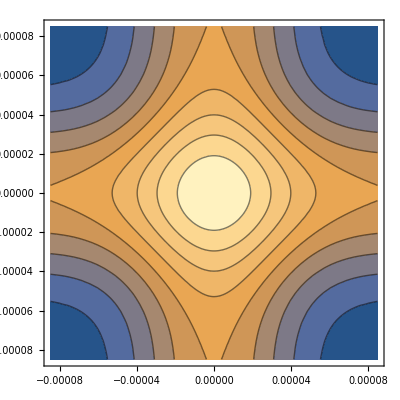

```mathematica
Clear["Global`*"]

(*Constants*)
c   =   QuantityMagnitude[Entity["PhysicalConstant","SpeedOfLight"]["Value"]];
e   =   QuantityMagnitude["ElectronCharge","SIBase"]//N;
Subscript[m, e] =   QuantityMagnitude[Entity["PhysicalConstant","ElectronMass"]["Value"]] ;
permittivity =   QuantityMagnitude["VacuumPermittivity","SIBase"]//N;

(*Wavelenght of light creating trapping potential*)
LambdaL = 1064*10^-9;  (*[m], laser wavelength*)
LambdaT =   461*10^-9;  (*[m], atomic transition wavelenght*)

(*Parameters for equations*)
Subscript[w, 0] =  60.0*10^-6/Sqrt[2];(* 60.0*10^-6/Sqrt[2]; *) (*m, this is defined as the e_raduouse not e^2*)
power = 7.0;                              (*W*)
m = 87 1.66054 10^-27;        (*Kg*)

ω   =  N[ c / LambdaL];           (*Hz*)
Subscript[ω, 0] =  N[ c / LambdaT ];          (*Hz*)
Γ = 32*10^6 ;

(*Rayleigh range*)
zR= (2 π Subscript[w, 0]^2)/LambdaL;
(*Print["The ratio 2zR^2/w_0^2 = ",2 zR^2/Subscript[w, 0]^2 ]*)

(*Spot size of the beam*)
w[z_] =Sqrt[2]  Subscript[w, 0] * Sqrt[  1 + (z/zR)^2];

(*Calculating Peak intensity from peak power*)
Subscript[I, 0] = power/(π Subscript[w, 0]^2);

(*Intensity as a function of position for a gaussian beam*)
Intensity[x_,y_, z_] = Subscript[I, 0] ((Sqrt[2] Subscript[w, 0])/w[z])^2  Exp[(-2*(x^2+ y^2))/w[z]^2];

(*Intensity[x_,y_, z_] = Intensity[y,z,x] + Intensity[ x,z,y];*)
Intensity[x_,y_, z_] = Intensity[z,x,y] +Intensity[z,y,x] 

GradIntensity = Grad[Intensity[x,y,z], {x,y,z}];
(*Print["the Grad(I) = ", GradIntensity /. {x->20.0*10^(-6),y->20*10^(-6),z->80.953*10^(-7)}]*)

(* Calculating  the  Polerizability *)
α = (3 π c^3 permittivity)/(2 π Subscript[ω, 0])^3( Γ/(Subscript[ω, 0]-ω) +Γ/(Subscript[ω, 0]+ω));

(* Potential energy function for a harmonic trap *)
U[x_, y_, z_] = (-1/(2permittivity c))α  Intensity[x,y, z];

wx[x_, y_, z_] = Sqrt[D[U[x,y,z], {x,2}]/m];
wy[x_, y_, z_] = Sqrt[D[U[x,y,z], {y,2}]/m];
wz[x_, y_, z_] = Sqrt[D[U[x,y,z], {z,2}]/m];

wx[0,0,0]
wy[0,0,0]
wz[0,0,0]

(*(*Calculating trap freq*)
Û= Abs[U[0, 0, 0]];
ωr = Sqrt [2 Û/(m Subscript[w, 0]^2)];
ωz = Sqrt [ 2Û/( m zR^2)];*)

(*Print ["ωr = ",  ωr];
Print ["ωz = ",  ωz];*)

(* Calculating force as a function of posistion *)
Force[x_,y_,z_] = -Grad[U[x,y,z], {x,y,z}];(*- 9.8 {0,0,1}*)

(*Plotting*)
(*DensityPlot[Intensity[x,y,0],{x,-0.0001,0.0001},{y,-0.0001,0.0001}]*)
ContourPlot[Intensity[x,y,0],{x,-2 Subscript[w, 0],2 Subscript[w, 0]},{y,-2 Subscript[w, 0],2 Subscript[w, 0]}]
```